{1.,1.41421,1.44225,1.41421,1.37973,1.34801,1.32047,1.29684,1.27652,1.25893,1.24358,1.23008,1.21811,1.20744,1.19786,1.18921,1.18135,1.17419,1.16762,1.16159,1.15601,1.15085,1.14606,1.14159,1.13741}

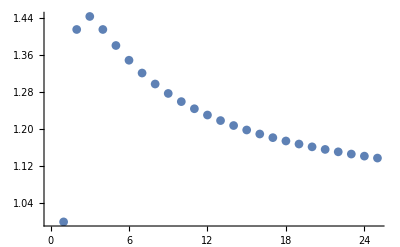

```mathematica
(* Name: Jenny Chen *)
(* MATH2262: Analytic Geometry and Calculus II *)
(* Mathematica Project 3 *)

(* PART I: pg.584: 137-148 *)

(* 137. Subscript[a, n]= n^(1/n) *)

(*a. *) a[n_]:=N[n^(1/n)];
		u=Table[a[n],{n,1,25}] 
ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(*b. *)
L= 1.64
N0= 21
Table[Abs[a[n]-L],{n,N0,25}]
```

1.64

21

{0.000911253,0.000481127,0.0000877733,0.00027333,0.000605994}

{1.5,1.5625,1.58796,1.60181,1.61051,1.61649,1.62085,1.62417,1.62678,1.62889,1.63063,1.63209,1.63334,1.6344,1.63533,1.63615,1.63687,1.63752,1.6381,1.63862,1.63909,1.63952,1.63991,1.64027,1.64061}

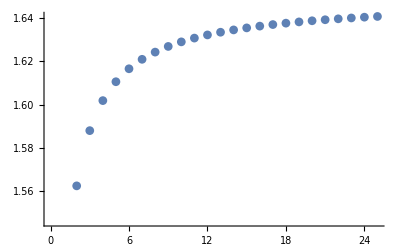

```mathematica
(* 138. Subscript[a, n] = (1 + 0.5/n)^n *)

(* a. *) a[n_]:=N[(1 + (0.5/n))^n];
		  u=Table[a[n],{n,1,25}]
		  ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(*b. *)
L= 1.64
N0= 21
Table[Abs[a[n]-L],{n,N0,25}]
```

1.64

21

{0.000911253,0.000481127,0.0000877733,0.00027333,0.000605994}

{1.,1.2,1.24,1.248,1.2496,1.24992,1.24998,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25}

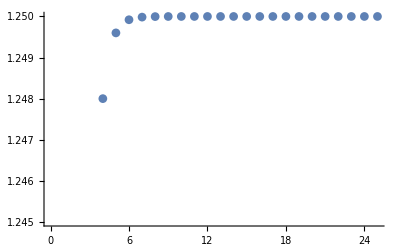

```mathematica
(* 139. Subscript[a, 1]= 1, Subscript[a, n+1]= Subscript[a, n] + 1/5^n *)
(* a. *) 
u=RecurrenceTable[{a[n+1]==N[a[n]+1/5^n],a[1]==1},a,{n,1,25}]
ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(*b. *)
L= 1
N0= 10
Table[Abs[u[[n]]-L],{n,N0,25}]
```

1

10

{0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

```mathematica
(* 140. Subscript[a, 1]= 1, Subscript[a, n+1]= Subscript[a, n] + (-2)^n *)
```

{1.,-1.,3.,-5.,11.,-21.,43.,-85.,171.,-341.,683.,-1365.,2731.,-5461.,10923.,-21845.,43691.,-87381.,174763.,-349525.,699051.,-1.3981×10^6,2.7962×10^6,-5.59241×10^6,1.11848×10^7}

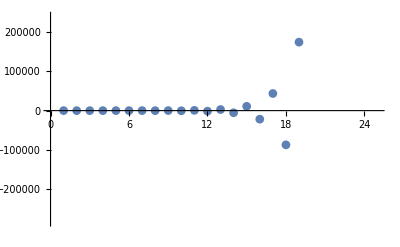

```mathematica
(* a. *)  u=RecurrenceTable[{a[n+1]==N[a[n]+(-2)^n],a[1]==1},a,{n,1,25}]
		ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(* b. *)
L= 1
N0= 10
Table[Abs[u[[n]]-L],{n,N0,25}]
(* 141. Subscript[a, n] = sin(n) *)
```

1

10

{342.,682.,1366.,2730.,5462.,10922.,21846.,43690.,87382.,174762.,349526.,699050.,1.3981×10^6,2.7962×10^6,5.59241×10^6,1.11848×10^7}

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021,-0.99999,-0.536573,0.420167,0.990607,0.650288,-0.287903,-0.961397,-0.750987,0.149877,0.912945,0.836656,-0.00885131,-0.84622,-0.905578,-0.132352}

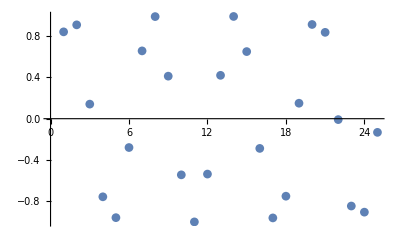

```mathematica
(* a. *) a[n_]:=N[Sin[n]];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

{0.841471,0.958851,0.981584,0.989616,0.993347,0.995377,0.996602,0.997398,0.997944,0.998334,0.998623,0.998843,0.999014,0.99915,0.999259,0.999349,0.999423,0.999486,0.999538,0.999583,0.999622,0.999656,0.999685,0.999711,0.999733}

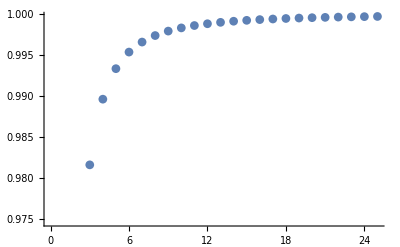

```mathematica
(* b. *)
(* Series diverges so there is no L *)

(* 142. Subscript[a, n] = n Sin[1/n] *)
(* a. *) a[n_]:=N[n*Sin[1/n]];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(*b. *)
L= 1
N0= 10
Table[Abs[a[n]-L],{n,N0,25}]
```

1

10

{0.00166583,0.00137684,0.00115701,0.000985902,0.000850123,0.000740576,0.000650915,0.000576602,0.000514324,0.000461617,0.000416615,0.000377886,0.000344317,0.00031503,0.000289327,0.000266645}

{0.841471,0.454649,0.04704,-0.189201,-0.191785,-0.0465692,0.0938552,0.12367,0.0457909,-0.0544021,-0.0909082,-0.0447144,0.0323205,0.0707577,0.0433525,-0.017994,-0.0565528,-0.0417215,0.00788827,0.0456473,0.0398407,-0.000402332,-0.0367922,-0.0377324,-0.00529407}

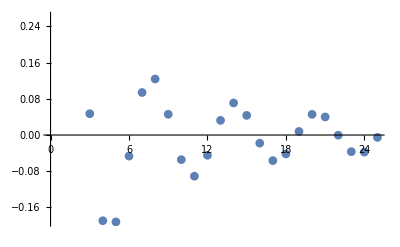

```mathematica
(* 143. Subscript[a, n] = Sin[n]/n *)
(* a. *) a[n_]:=N[Sin[n]/n];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(*b. *)
```

{0.,0.346574,0.366204,0.346574,0.321888,0.298627,0.277987,0.25993,0.244136,0.230259,0.21799,0.207076,0.197304,0.188504,0.180537,0.173287,0.16666,0.160576,0.15497,0.149787,0.144977,0.140502,0.136326,0.132419,0.128755}

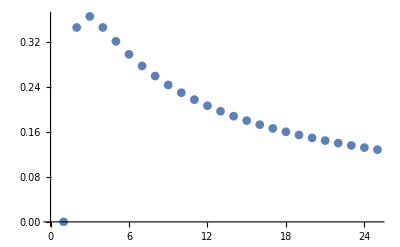

```mathematica
(* Series diverges so there is no L *)

(* 144. Subscript[a, n] = Log[n]/n*)
(* a. *) a[n_]:=N[Log[n]/n];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(* b. *)
```

```mathematica
L= .15
N0= 10
Table[Abs[a[n]-L],{n,N0,25}]
```

0.15

10

{0.0802585,0.0679905,0.0570756,0.0473038,0.0385041,0.0305367,0.0232868,0.0166596,0.0105762,0.00497047,0.000213386,0.00502274,0.00949807,0.0136742,0.0175811,0.021245}

{0.9999,0.9998,0.9997,0.9996,0.9995,0.9994,0.9993,0.9992,0.9991,0.999,0.998901,0.998801,0.998701,0.998601,0.998501,0.998401,0.998301,0.998202,0.998102,0.998002,0.997902,0.997802,0.997703,0.997603,0.997503}

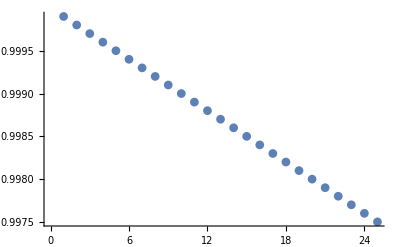

```mathematica
(* 145. Subscript[a, n] = (0.9999)^n *)
(* a. *) a[n_]:=N[(0.9999)^n];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(* b. *)
```

```mathematica
L= 1
N0= 10
Table[Abs[a[n]-L],{n,N0,25}]
```

1

10

{0.00099955,0.00109945,0.00119934,0.00129922,0.00139909,0.00149895,0.0015988,0.00169864,0.00179847,0.00189829,0.0019981,0.0020979,0.00219769,0.00229747,0.00239724,0.002497}

{123456.,351.363,49.7933,18.7447,10.4304,7.05644,5.33776,4.32951,3.67895,3.22962,2.90312,2.6564,2.46408,2.31036,2.18491,2.08075,1.99297,1.91806,1.85342,1.79711,1.74764,1.70385,1.66483,1.62985,1.59831}

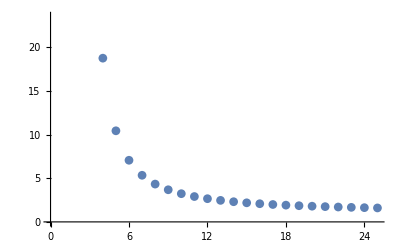

```mathematica
(* 146. Subscript[a, n] = (123456)^(1/n) *)
(* a. *) a[n_]:=N[(123456)^(1/n)];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

{8.,32.,85.3333,170.667,273.067,364.089,416.102,416.102,369.868,295.894,215.196,143.464,88.2855,50.4489,26.9061,13.453,6.33084,2.81371,1.18472,0.473887,0.180529,0.0656467,0.0228336,0.00761122,0.00243559}

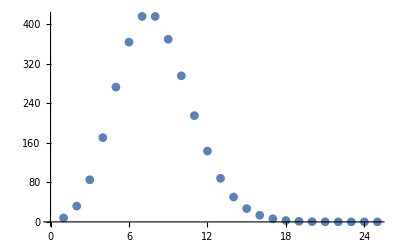

```mathematica
(* b. *)
(* Series diverges so there is no L *)

(* 147. Subscript[a, n] = ((8^n)/(n!)) *)
(* a. *)  a[n_]:=N[(8^n)/(n!)];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(* b. *)
```

```mathematica
L= ⅇ^8
N0= 20
Table[Abs[a[n]-L],{n,N0,25}]
```

ⅇ^8

20

{5.85003×10^27,2.27596×10^27,8.06772×10^26,2.62729×10^26,7.91725×10^25,2.22178×10^25}

```mathematica
(* 148. Subscript[a, n] = (n^41)/(19^n) *)
(* a. *) a[n_]:=N[(n^41)/(19^n)];
		u=Table[a[n],{n,1,25}] 
		ListPlot[u,PlotMarkers->Automatic]
```

{0.0526316,6.09148×10^9,5.31754×10^15,3.71061×10^19,1.83655×10^22,1.70482×10^24,4.98591×10^25,6.26124×10^26,4.1225×10^27,1.63104×10^28,4.27376×10^28,7.96871×10^28,1.11656×10^29,1.22659×10^29,1.09254×10^29,8.10703×10^28,5.12383×10^28,2.80936×10^28,1.357×10^28,5.85003×10^27,2.27596×10^27,8.06772×10^26,2.62729×10^26,7.91725×10^25,2.22178×10^25}

-Graphics-

```mathematica
(* b. *)
L= 1/19
N0= 20
Table[Abs[a[n]-L],{n,N0,25}]
```

1/19

20

{5.85003×10^27,2.27596×10^27,8.06772×10^26,2.62729×10^26,7.91725×10^25,2.22178×10^25}

1+2 x

1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+(4 x^5)/15

1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+(4 x^5)/15+(4 x^6)/45+(8 x^7)/315+(2 x^8)/315+(4 x^9)/2835+(4 x^10)/14175+(8 x^11)/155925+(4 x^12)/467775+(8 x^13)/6081075+(8 x^14)/42567525+(16 x^15)/638512875

1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+(4 x^5)/15+(4 x^6)/45+(8 x^7)/315+(2 x^8)/315+(4 x^9)/2835+(4 x^10)/14175+(8 x^11)/155925+(4 x^12)/467775+(8 x^13)/6081075+(8 x^14)/42567525+(16 x^15)/638512875+(2 x^16)/638512875+(4 x^17)/10854718875+(4 x^18)/97692469875+(8 x^19)/1856156927625+(4 x^20)/9280784638125

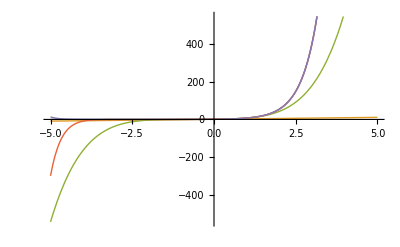

```mathematica
(* PART II: pg. 630: 1-32 *)

(* 1. f(x) = ⅇ^(2x) *)
Clear[f,P1,P2,P3,x]
f[x_]:=ⅇ^(2x);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-5,5},PlotStyle->Thick]
```

x

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000

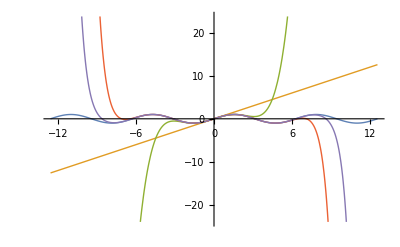

```mathematica
(* 2. f(x) = Sin[x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Sin[x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4*Pi,4*Pi},PlotStyle->Thick]
```

-1+x

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5+x

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5-1/6 (-1+x)^6+1/7 (-1+x)^7-1/8 (-1+x)^8+1/9 (-1+x)^9-1/10 (-1+x)^10+1/11 (-1+x)^11-1/12 (-1+x)^12+1/13 (-1+x)^13-1/14 (-1+x)^14+1/15 (-1+x)^15+x

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5-1/6 (-1+x)^6+1/7 (-1+x)^7-1/8 (-1+x)^8+1/9 (-1+x)^9-1/10 (-1+x)^10+1/11 (-1+x)^11-1/12 (-1+x)^12+1/13 (-1+x)^13-1/14 (-1+x)^14+1/15 (-1+x)^15-1/16 (-1+x)^16+1/17 (-1+x)^17-1/18 (-1+x)^18+1/19 (-1+x)^19-1/20 (-1+x)^20+x

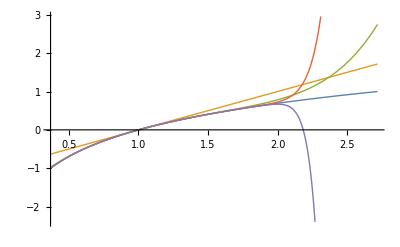

```mathematica
(* 3. f(x) = Log[x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Log[E, x];
c=1;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,.3678,2.7182},PlotStyle->Thick]
```

x

x-x^2/2+x^3/3-x^4/4+x^5/5

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15-x^16/16+x^17/17-x^18/18+x^19/19-x^20/20

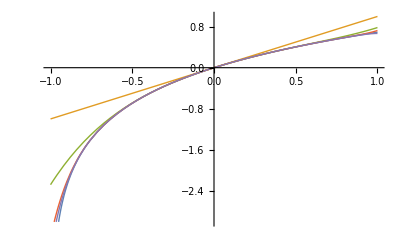

```mathematica
(* 4. f(x) = Log[1 + x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Log[1 +x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-1,1},PlotStyle->Thick]
```

1/2+(2-x)/4

1/2+(2-x)/4+1/8 (-2+x)^2-1/16 (-2+x)^3+1/32 (-2+x)^4-1/64 (-2+x)^5

1/2+(2-x)/4+1/8 (-2+x)^2-1/16 (-2+x)^3+1/32 (-2+x)^4-1/64 (-2+x)^5+1/128 (-2+x)^6-1/256 (-2+x)^7+1/512 (-2+x)^8-(-2+x)^9/1024+(-2+x)^10/2048-(-2+x)^11/4096+(-2+x)^12/8192-(-2+x)^13/16384+(-2+x)^14/32768-(-2+x)^15/65536

1/2+(2-x)/4+1/8 (-2+x)^2-1/16 (-2+x)^3+1/32 (-2+x)^4-1/64 (-2+x)^5+1/128 (-2+x)^6-1/256 (-2+x)^7+1/512 (-2+x)^8-(-2+x)^9/1024+(-2+x)^10/2048-(-2+x)^11/4096+(-2+x)^12/8192-(-2+x)^13/16384+(-2+x)^14/32768-(-2+x)^15/65536+(-2+x)^16/131072-(-2+x)^17/262144+(-2+x)^18/524288-(-2+x)^19/1048576+(-2+x)^20/2097152

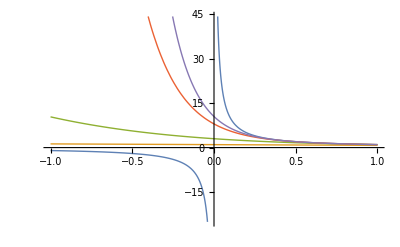

```mathematica
(* 5. f(x) = 1/x *)
Clear[f,P1,P2,P3,x]
f[x_]:=1/x;
c=2;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-1,1},PlotStyle->Thick]
```

1/2-x/4

1/2-x/4+x^2/8-x^3/16+x^4/32-x^5/64

1/2-x/4+x^2/8-x^3/16+x^4/32-x^5/64+x^6/128-x^7/256+x^8/512-x^9/1024+x^10/2048-x^11/4096+x^12/8192-x^13/16384+x^14/32768-x^15/65536

1/2-x/4+x^2/8-x^3/16+x^4/32-x^5/64+x^6/128-x^7/256+x^8/512-x^9/1024+x^10/2048-x^11/4096+x^12/8192-x^13/16384+x^14/32768-x^15/65536+x^16/131072-x^17/262144+x^18/524288-x^19/1048576+x^20/2097152

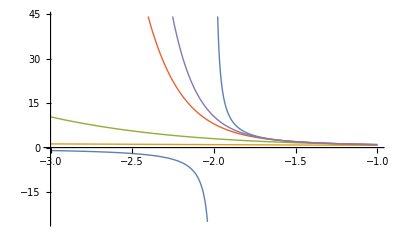

```mathematica
(* 6. f(x) = 1/(x+2) *)
Clear[f,P1,P2,P3,x]
f[x_]:=1/(x+2);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-3,-1},PlotStyle->Thick]
```

1/(√2)+(-π/4+x)/(√2)

1/(√2)+(-π/4+x)/(√2)-(-π/4+x)^2/(2 √2)-(-π/4+x)^3/(6 √2)+(-π/4+x)^4/(24 √2)+(-π/4+x)^5/(120 √2)

1/(√2)+(-π/4+x)/(√2)-(-π/4+x)^2/(2 √2)-(-π/4+x)^3/(6 √2)+(-π/4+x)^4/(24 √2)+(-π/4+x)^5/(120 √2)-(-π/4+x)^6/(720 √2)-(-π/4+x)^7/(5040 √2)+(-π/4+x)^8/(40320 √2)+(-π/4+x)^9/(362880 √2)-(-π/4+x)^10/(3628800 √2)-(-π/4+x)^11/(39916800 √2)+(-π/4+x)^12/(479001600 √2)+(-π/4+x)^13/(6227020800 √2)-(-π/4+x)^14/(87178291200 √2)-(-π/4+x)^15/(1307674368000 √2)

1/(√2)+(-π/4+x)/(√2)-(-π/4+x)^2/(2 √2)-(-π/4+x)^3/(6 √2)+(-π/4+x)^4/(24 √2)+(-π/4+x)^5/(120 √2)-(-π/4+x)^6/(720 √2)-(-π/4+x)^7/(5040 √2)+(-π/4+x)^8/(40320 √2)+(-π/4+x)^9/(362880 √2)-(-π/4+x)^10/(3628800 √2)-(-π/4+x)^11/(39916800 √2)+(-π/4+x)^12/(479001600 √2)+(-π/4+x)^13/(6227020800 √2)-(-π/4+x)^14/(87178291200 √2)-(-π/4+x)^15/(1307674368000 √2)+(-π/4+x)^16/(20922789888000 √2)+(-π/4+x)^17/(355687428096000 √2)-(-π/4+x)^18/(6402373705728000 √2)-(-π/4+x)^19/(121645100408832000 √2)+(-π/4+x)^20/(2432902008176640000 √2)

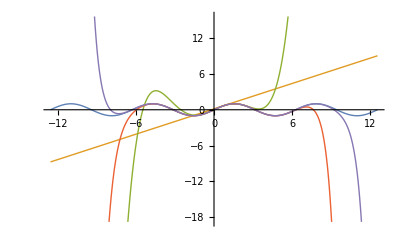

```mathematica
(* 7. f(x) = Sin[x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=  Sin[x];
c=Pi/4;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4*Pi,4*Pi},PlotStyle->Thick]
```

1+2 (-π/4+x)

1+2 (-π/4+x)+2 (-π/4+x)^2+8/3 (-π/4+x)^3+10/3 (-π/4+x)^4+64/15 (-π/4+x)^5

1+2 (-π/4+x)+2 (-π/4+x)^2+8/3 (-π/4+x)^3+10/3 (-π/4+x)^4+64/15 (-π/4+x)^5+244/45 (-π/4+x)^6+2176/315 (-π/4+x)^7+554/63 (-π/4+x)^8+(31744 (-π/4+x)^9)/2835+(202084 (-π/4+x)^10)/14175+(2830336 (-π/4+x)^11)/155925+(2162212 (-π/4+x)^12)/93555+(178946048 (-π/4+x)^13)/6081075+(1594887848 (-π/4+x)^14)/42567525+(30460116992 (-π/4+x)^15)/638512875

1+2 (-π/4+x)+2 (-π/4+x)^2+8/3 (-π/4+x)^3+10/3 (-π/4+x)^4+64/15 (-π/4+x)^5+244/45 (-π/4+x)^6+2176/315 (-π/4+x)^7+554/63 (-π/4+x)^8+(31744 (-π/4+x)^9)/2835+(202084 (-π/4+x)^10)/14175+(2830336 (-π/4+x)^11)/155925+(2162212 (-π/4+x)^12)/93555+(178946048 (-π/4+x)^13)/6081075+(1594887848 (-π/4+x)^14)/42567525+(30460116992 (-π/4+x)^15)/638512875+(7756604858 (-π/4+x)^16)/127702575+(839461371904 (-π/4+x)^17)/10854718875+(9619518701764 (-π/4+x)^18)/97692469875+(232711080902656 (-π/4+x)^19)/1856156927625+(59259390118004 (-π/4+x)^20)/371231385525

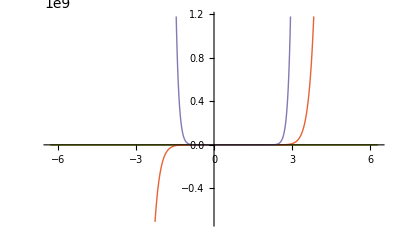

```mathematica
(* 8. f(x) = Tan[x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Tan[x];
c=Pi/4;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-2*Pi,2*Pi},PlotStyle->Thick]
```

2+1/4 (-4+x)

2+1/4 (-4+x)-1/64 (-4+x)^2+1/512 (-4+x)^3-(5 (-4+x)^4)/16384+(7 (-4+x)^5)/131072

2+1/4 (-4+x)-1/64 (-4+x)^2+1/512 (-4+x)^3-(5 (-4+x)^4)/16384+(7 (-4+x)^5)/131072-(21 (-4+x)^6)/2097152+(33 (-4+x)^7)/16777216-(429 (-4+x)^8)/1073741824+(715 (-4+x)^9)/8589934592-(2431 (-4+x)^10)/137438953472+(4199 (-4+x)^11)/1099511627776-(29393 (-4+x)^12)/35184372088832+(52003 (-4+x)^13)/281474976710656-(185725 (-4+x)^14)/4503599627370496+(334305 (-4+x)^15)/36028797018963968

2+1/4 (-4+x)-1/64 (-4+x)^2+1/512 (-4+x)^3-(5 (-4+x)^4)/16384+(7 (-4+x)^5)/131072-(21 (-4+x)^6)/2097152+(33 (-4+x)^7)/16777216-(429 (-4+x)^8)/1073741824+(715 (-4+x)^9)/8589934592-(2431 (-4+x)^10)/137438953472+(4199 (-4+x)^11)/1099511627776-(29393 (-4+x)^12)/35184372088832+(52003 (-4+x)^13)/281474976710656-(185725 (-4+x)^14)/4503599627370496+(334305 (-4+x)^15)/36028797018963968-(9694845 (-4+x)^16)/4611686018427387904+(17678835 (-4+x)^17)/36893488147419103232-(64822395 (-4+x)^18)/590295810358705651712+(119409675 (-4+x)^19)/4722366482869645213696-(883631595 (-4+x)^20)/151115727451828646838272

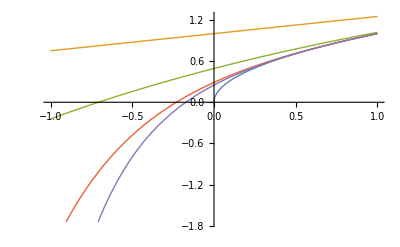

```mathematica
(* 9. f(x) = Sqrt[x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Sqrt[x];
c=4;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-1,1},PlotStyle->Thick]
```

1-x/2

1-x/2-x^2/8-x^3/16-(5 x^4)/128-(7 x^5)/256

1-x/2-x^2/8-x^3/16-(5 x^4)/128-(7 x^5)/256-(21 x^6)/1024-(33 x^7)/2048-(429 x^8)/32768-(715 x^9)/65536-(2431 x^10)/262144-(4199 x^11)/524288-(29393 x^12)/4194304-(52003 x^13)/8388608-(185725 x^14)/33554432-(334305 x^15)/67108864

1-x/2-x^2/8-x^3/16-(5 x^4)/128-(7 x^5)/256-(21 x^6)/1024-(33 x^7)/2048-(429 x^8)/32768-(715 x^9)/65536-(2431 x^10)/262144-(4199 x^11)/524288-(29393 x^12)/4194304-(52003 x^13)/8388608-(185725 x^14)/33554432-(334305 x^15)/67108864-(9694845 x^16)/2147483648-(17678835 x^17)/4294967296-(64822395 x^18)/17179869184-(119409675 x^19)/34359738368-(883631595 x^20)/274877906944

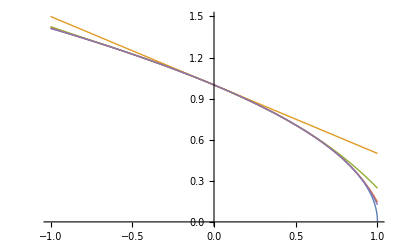

```mathematica
(* 10. f(x) = Sqrt[1 - x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Sqrt[1 - x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-1,1},PlotStyle->Thick]
```

1-x

1-x+x^2/2-x^3/6+x^4/24-x^5/120

1-x+x^2/2-x^3/6+x^4/24-x^5/120+x^6/720-x^7/5040+x^8/40320-x^9/362880+x^10/3628800-x^11/39916800+x^12/479001600-x^13/6227020800+x^14/87178291200-x^15/1307674368000

1-x+x^2/2-x^3/6+x^4/24-x^5/120+x^6/720-x^7/5040+x^8/40320-x^9/362880+x^10/3628800-x^11/39916800+x^12/479001600-x^13/6227020800+x^14/87178291200-x^15/1307674368000+x^16/20922789888000-x^17/355687428096000+x^18/6402373705728000-x^19/121645100408832000+x^20/2432902008176640000

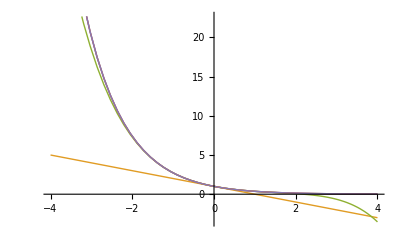

```mathematica
(* 11. ⅇ^(-x) *)
Clear[f,P1,P2,P3,x]
f[x_]:= ⅇ^(-x);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4,4},PlotStyle->Thick]
```

x

x+x^2+x^3/2+x^4/6+x^5/24

x+x^2+x^3/2+x^4/6+x^5/24+x^6/120+x^7/720+x^8/5040+x^9/40320+x^10/362880+x^11/3628800+x^12/39916800+x^13/479001600+x^14/6227020800+x^15/87178291200

x+x^2+x^3/2+x^4/6+x^5/24+x^6/120+x^7/720+x^8/5040+x^9/40320+x^10/362880+x^11/3628800+x^12/39916800+x^13/479001600+x^14/6227020800+x^15/87178291200+x^16/1307674368000+x^17/20922789888000+x^18/355687428096000+x^19/6402373705728000+x^20/121645100408832000

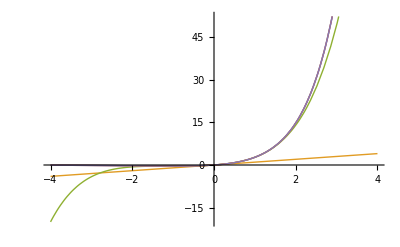

```mathematica
(* 12. xⅇ^(x) *)
Clear[f,P1,P2,P3,x]
f[x_]:= x*ⅇ^(x);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4,4},PlotStyle->Thick]
```

1-x

1-x+x^2-x^3+x^4-x^5

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15+x^16-x^17+x^18-x^19+x^20

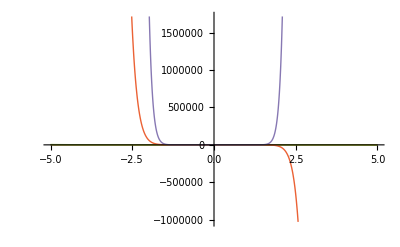

```mathematica
(* 13. 1/(1 + x) *)
Clear[f,P1,P2,P3,x]
f[x_]:=1/(1+x);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-5,5},PlotStyle->Thick]
```

2+3 x

2+3 x+3 x^2+3 x^3+3 x^4+3 x^5

2+3 x+3 x^2+3 x^3+3 x^4+3 x^5+3 x^6+3 x^7+3 x^8+3 x^9+3 x^10+3 x^11+3 x^12+3 x^13+3 x^14+3 x^15

2+3 x+3 x^2+3 x^3+3 x^4+3 x^5+3 x^6+3 x^7+3 x^8+3 x^9+3 x^10+3 x^11+3 x^12+3 x^13+3 x^14+3 x^15+3 x^16+3 x^17+3 x^18+3 x^19+3 x^20

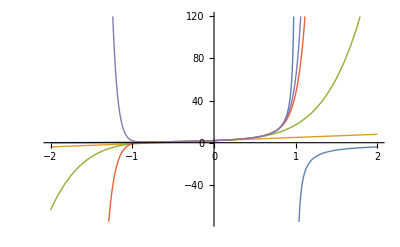

```mathematica
(* 14. (2+x)/(1-x) *)
Clear[f,P1,P2,P3,x]
f[x_]:=(2+x)/(1-x);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-2,2},PlotStyle->Thick]
```

3 x

3 x-(9 x^3)/2+(81 x^5)/40

3 x-(9 x^3)/2+(81 x^5)/40-(243 x^7)/560+(243 x^9)/4480-(2187 x^11)/492800+(6561 x^13)/25625600-(19683 x^15)/1793792000

3 x-(9 x^3)/2+(81 x^5)/40-(243 x^7)/560+(243 x^9)/4480-(2187 x^11)/492800+(6561 x^13)/25625600-(19683 x^15)/1793792000+(177147 x^17)/487911424000-(177147 x^19)/18540634112000

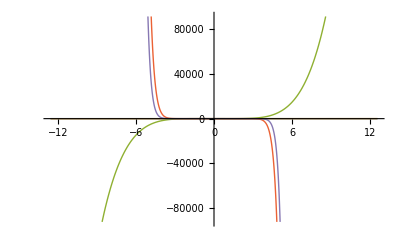

```mathematica
(* 15. Sin[3x] *)
Clear[f,P1,P2,P3,x]
f[x_]:= Sin[3x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4*Pi,4*Pi},PlotStyle->Thick]
```

x/2

x/2-x^3/48+x^5/3840

x/2-x^3/48+x^5/3840-x^7/645120+x^9/185794560-x^11/81749606400+x^13/51011754393600-x^15/42849873690624000

x/2-x^3/48+x^5/3840-x^7/645120+x^9/185794560-x^11/81749606400+x^13/51011754393600-x^15/42849873690624000+x^17/46620662575398912000-x^19/63777066403145711616000

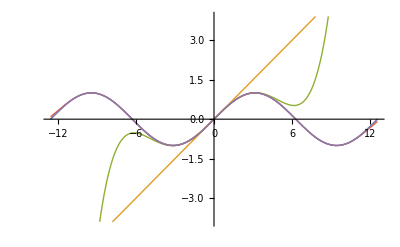

```mathematica
(* 16. Sin[x/2] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Sin[x/2];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4*Pi,4*Pi},PlotStyle->Thick]
```

7

7-(7 x^2)/2+(7 x^4)/24

7-(7 x^2)/2+(7 x^4)/24-(7 x^6)/720+x^8/5760-x^10/518400+x^12/68428800-x^14/12454041600

7-(7 x^2)/2+(7 x^4)/24-(7 x^6)/720+x^8/5760-x^10/518400+x^12/68428800-x^14/12454041600+x^16/2988969984000-x^18/914624815104000+x^20/347557429739520000

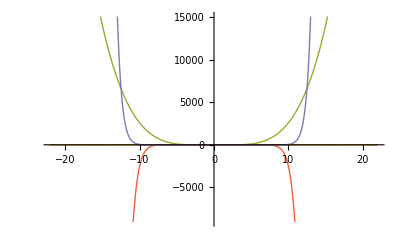

```mathematica
(* 17. 7Cos[-x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=7Cos[-x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-7*Pi,7*Pi},PlotStyle->Thick]
```

5

5-(5 π^2 x^2)/2+(5 π^4 x^4)/24

5-(5 π^2 x^2)/2+(5 π^4 x^4)/24-(π^6 x^6)/144+(π^8 x^8)/8064-(π^10 x^10)/725760+(π^12 x^12)/95800320-(π^14 x^14)/17435658240

5-(5 π^2 x^2)/2+(5 π^4 x^4)/24-(π^6 x^6)/144+(π^8 x^8)/8064-(π^10 x^10)/725760+(π^12 x^12)/95800320-(π^14 x^14)/17435658240+(π^16 x^16)/4184557977600-(π^18 x^18)/1280474741145600+(π^20 x^20)/486580401635328000

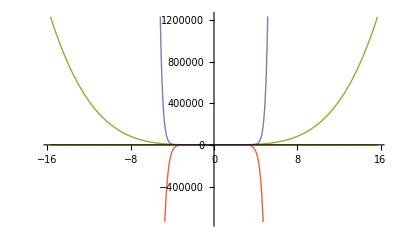

```mathematica
(* 18. 5Cos[Pi*x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=5 Cos[Pi * x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-5*Pi,5*Pi},PlotStyle->Thick]
```

1

1+x^2/2+x^4/24

1+x^2/2+x^4/24+x^6/720+x^8/40320+x^10/3628800+x^12/479001600+x^14/87178291200

1+x^2/2+x^4/24+x^6/720+x^8/40320+x^10/3628800+x^12/479001600+x^14/87178291200+x^16/20922789888000+x^18/6402373705728000+x^20/2432902008176640000

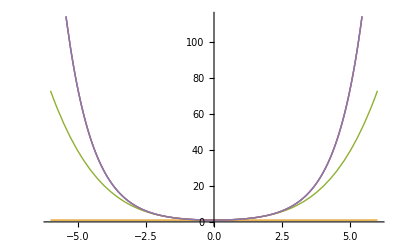

```mathematica
(* 19. Cosh x = (ⅇ^x + ⅇ^(-x))/2 *)
Clear[f,P1,P2,P3,x]
f[x_]:= (ⅇ^x + ⅇ^(-x))/2;
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-6,6},PlotStyle->Thick]
```

x

x+x^3/6+x^5/120

x+x^3/6+x^5/120+x^7/5040+x^9/362880+x^11/39916800+x^13/6227020800+x^15/1307674368000

x+x^3/6+x^5/120+x^7/5040+x^9/362880+x^11/39916800+x^13/6227020800+x^15/1307674368000+x^17/355687428096000+x^19/121645100408832000

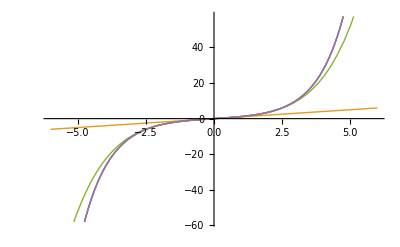

```mathematica
(* 20. Sinh x = (ⅇ^x - ⅇ^(-x))/2 *)
Clear[f,P1,P2,P3,x]
f[x_]:= (ⅇ^x - ⅇ^(-x))/2;
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-6,6},PlotStyle->Thick]
```

4-5 x

4-5 x-2 x^3+x^4

4-5 x-2 x^3+x^4

4-5 x-2 x^3+x^4

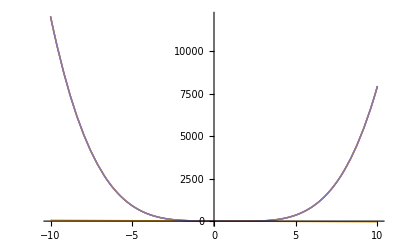

```mathematica
(* 21. x^4-2x^3-5x+4 *)
Clear[f,P1,P2,P3,x]
f[x_]:= x^4-2x^3-5x+4;
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-10,10},PlotStyle->Thick]
```

0

x^2-x^3+x^4-x^5

x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15

x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15+x^16-x^17+x^18-x^19+x^20

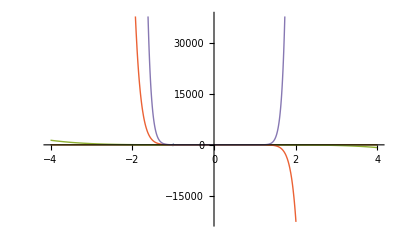

```mathematica
(* 22. (x^2)/(x+1) *)
Clear[f,P1,P2,P3,x]
f[x_]:= (x^2)/(x+1);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4,4},PlotStyle->Thick]
```

8+10 (-2+x)

8+10 (-2+x)+6 (-2+x)^2+(-2+x)^3

8+10 (-2+x)+6 (-2+x)^2+(-2+x)^3

8+10 (-2+x)+6 (-2+x)^2+(-2+x)^3

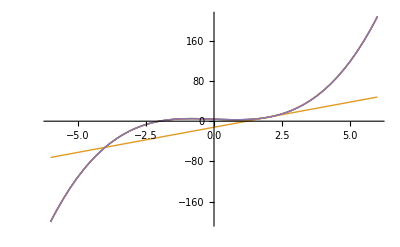

```mathematica
(* 23. f(x) = x^3-2x+4 *)
Clear[f,P1,P2,P3,x]
f[x_]:= x^3-2x+4;
c=2;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-6,6},PlotStyle->Thick]
```

-2+11 (-1+x)

-2+11 (-1+x)+7 (-1+x)^2+2 (-1+x)^3

-2+11 (-1+x)+7 (-1+x)^2+2 (-1+x)^3

-2+11 (-1+x)+7 (-1+x)^2+2 (-1+x)^3

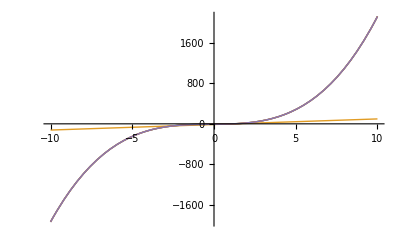

```mathematica
(* 24. f(x) = 2x^3+x^2+3x-8 *)
Clear[f,P1,P2,P3,x]
f[x_]:= 2x^3+x^2+3x-8
c=1;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-10,10},PlotStyle->Thick]
```

21+36 (-2+x)

21+36 (-2+x)+25 (-2+x)^2+8 (-2+x)^3+(-2+x)^4

21+36 (-2+x)+25 (-2+x)^2+8 (-2+x)^3+(-2+x)^4

21+36 (-2+x)+25 (-2+x)^2+8 (-2+x)^3+(-2+x)^4

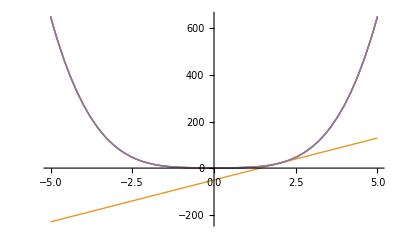

```mathematica
(* 25. f(x) = x^4 + x^2 + 1 *)
Clear[f,P1,P2,P3,x]
f[x_]:= x^4 + x^2 + 1;
c=2;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-5,5},PlotStyle->Thick]
```

-5+15 (1+x)

-5+15 (1+x)-29 (1+x)^2+28 (1+x)^3-14 (1+x)^4+3 (1+x)^5

-5+15 (1+x)-29 (1+x)^2+28 (1+x)^3-14 (1+x)^4+3 (1+x)^5

-5+15 (1+x)-29 (1+x)^2+28 (1+x)^3-14 (1+x)^4+3 (1+x)^5

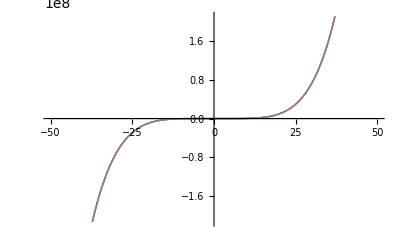

```mathematica
(* 26. f(x)= 3x^5-x^4+2x^3+x^2-2 *)
Clear[f,P1,P2,P3,x]
f[x_]:= 3x^5 + x^4 + 2x^3 + x^2-2;
c=-1;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-50,50},PlotStyle->Thick]
```

1-2 (-1+x)

1-2 (-1+x)+3 (-1+x)^2-4 (-1+x)^3+5 (-1+x)^4-6 (-1+x)^5

1-2 (-1+x)+3 (-1+x)^2-4 (-1+x)^3+5 (-1+x)^4-6 (-1+x)^5+7 (-1+x)^6-8 (-1+x)^7+9 (-1+x)^8-10 (-1+x)^9+11 (-1+x)^10-12 (-1+x)^11+13 (-1+x)^12-14 (-1+x)^13+15 (-1+x)^14-16 (-1+x)^15

1-2 (-1+x)+3 (-1+x)^2-4 (-1+x)^3+5 (-1+x)^4-6 (-1+x)^5+7 (-1+x)^6-8 (-1+x)^7+9 (-1+x)^8-10 (-1+x)^9+11 (-1+x)^10-12 (-1+x)^11+13 (-1+x)^12-14 (-1+x)^13+15 (-1+x)^14-16 (-1+x)^15+17 (-1+x)^16-18 (-1+x)^17+19 (-1+x)^18-20 (-1+x)^19+21 (-1+x)^20

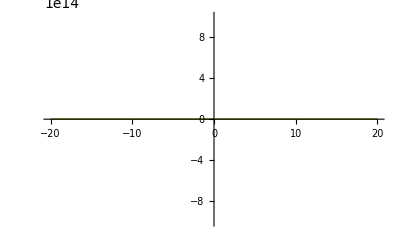

```mathematica
(* 27. f(x) = 1/x^2 *)
Clear[f,P1,P2,P3,x]
f[x_]:= 1/x^2;
c=1;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-20,20},PlotStyle->Thick]
```

1+3 x

1+3 x+6 x^2+10 x^3+15 x^4+21 x^5

1+3 x+6 x^2+10 x^3+15 x^4+21 x^5+28 x^6+36 x^7+45 x^8+55 x^9+66 x^10+78 x^11+91 x^12+105 x^13+120 x^14+136 x^15

1+3 x+6 x^2+10 x^3+15 x^4+21 x^5+28 x^6+36 x^7+45 x^8+55 x^9+66 x^10+78 x^11+91 x^12+105 x^13+120 x^14+136 x^15+153 x^16+171 x^17+190 x^18+210 x^19+231 x^20

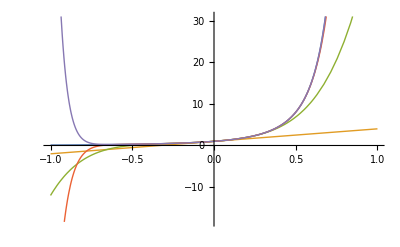

```mathematica
(* 28. f(x) = 1/((1-x)^3) *)
 Clear[f,P1,P2,P3,x]
f[x_]:= 1/((1-x)^3);
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-1,1},PlotStyle->Thick]
```

ⅇ^2+ⅇ^2 (-2+x)

ⅇ^2+ⅇ^2 (-2+x)+1/2 ⅇ^2 (-2+x)^2+1/6 ⅇ^2 (-2+x)^3+1/24 ⅇ^2 (-2+x)^4+1/120 ⅇ^2 (-2+x)^5

ⅇ^2+ⅇ^2 (-2+x)+1/2 ⅇ^2 (-2+x)^2+1/6 ⅇ^2 (-2+x)^3+1/24 ⅇ^2 (-2+x)^4+1/120 ⅇ^2 (-2+x)^5+1/720 ⅇ^2 (-2+x)^6+(ⅇ^2 (-2+x)^7)/5040+(ⅇ^2 (-2+x)^8)/40320+(ⅇ^2 (-2+x)^9)/362880+(ⅇ^2 (-2+x)^10)/3628800+(ⅇ^2 (-2+x)^11)/39916800+(ⅇ^2 (-2+x)^12)/479001600+(ⅇ^2 (-2+x)^13)/6227020800+(ⅇ^2 (-2+x)^14)/87178291200+(ⅇ^2 (-2+x)^15)/1307674368000

ⅇ^2+ⅇ^2 (-2+x)+1/2 ⅇ^2 (-2+x)^2+1/6 ⅇ^2 (-2+x)^3+1/24 ⅇ^2 (-2+x)^4+1/120 ⅇ^2 (-2+x)^5+1/720 ⅇ^2 (-2+x)^6+(ⅇ^2 (-2+x)^7)/5040+(ⅇ^2 (-2+x)^8)/40320+(ⅇ^2 (-2+x)^9)/362880+(ⅇ^2 (-2+x)^10)/3628800+(ⅇ^2 (-2+x)^11)/39916800+(ⅇ^2 (-2+x)^12)/479001600+(ⅇ^2 (-2+x)^13)/6227020800+(ⅇ^2 (-2+x)^14)/87178291200+(ⅇ^2 (-2+x)^15)/1307674368000+(ⅇ^2 (-2+x)^16)/20922789888000+(ⅇ^2 (-2+x)^17)/355687428096000+(ⅇ^2 (-2+x)^18)/6402373705728000+(ⅇ^2 (-2+x)^19)/121645100408832000+(ⅇ^2 (-2+x)^20)/2432902008176640000

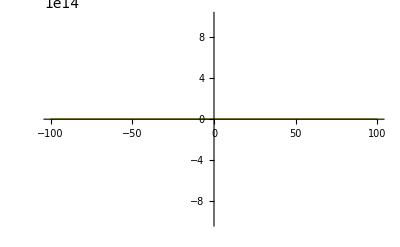

```mathematica
(* 29. ⅇ^x *)
Clear[f,P1,P2,P3,x]
f[x_]:= ⅇ^x;
c=2;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-100,100},PlotStyle->Thick]
```

2+2 (-1+x) Log[2]

2+2 (-1+x) Log[2]+(-1+x)^2 Log[2]^2+1/3 (-1+x)^3 Log[2]^3+1/12 (-1+x)^4 Log[2]^4+1/60 (-1+x)^5 Log[2]^5

2+2 (-1+x) Log[2]+(-1+x)^2 Log[2]^2+1/3 (-1+x)^3 Log[2]^3+1/12 (-1+x)^4 Log[2]^4+1/60 (-1+x)^5 Log[2]^5+1/360 (-1+x)^6 Log[2]^6+((-1+x)^7 Log[2]^7)/2520+((-1+x)^8 Log[2]^8)/20160+((-1+x)^9 Log[2]^9)/181440+((-1+x)^10 Log[2]^10)/1814400+((-1+x)^11 Log[2]^11)/19958400+((-1+x)^12 Log[2]^12)/239500800+((-1+x)^13 Log[2]^13)/3113510400+((-1+x)^14 Log[2]^14)/43589145600+((-1+x)^15 Log[2]^15)/653837184000

2+2 (-1+x) Log[2]+(-1+x)^2 Log[2]^2+1/3 (-1+x)^3 Log[2]^3+1/12 (-1+x)^4 Log[2]^4+1/60 (-1+x)^5 Log[2]^5+1/360 (-1+x)^6 Log[2]^6+((-1+x)^7 Log[2]^7)/2520+((-1+x)^8 Log[2]^8)/20160+((-1+x)^9 Log[2]^9)/181440+((-1+x)^10 Log[2]^10)/1814400+((-1+x)^11 Log[2]^11)/19958400+((-1+x)^12 Log[2]^12)/239500800+((-1+x)^13 Log[2]^13)/3113510400+((-1+x)^14 Log[2]^14)/43589145600+((-1+x)^15 Log[2]^15)/653837184000+((-1+x)^16 Log[2]^16)/10461394944000+((-1+x)^17 Log[2]^17)/177843714048000+((-1+x)^18 Log[2]^18)/3201186852864000+((-1+x)^19 Log[2]^19)/60822550204416000+((-1+x)^20 Log[2]^20)/1216451004088320000

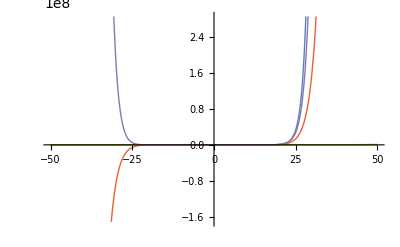

```mathematica
(* 30. f(x) = 2^x *)
Clear[f,P1,P2,P3,x]
f[x_]:= 2^x;
c=1;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-50,50},PlotStyle->Thick]
```

-1

-1+2 (-π/4+x)^2-2/3 (-π/4+x)^4

-1+2 (-π/4+x)^2-2/3 (-π/4+x)^4+4/45 (-π/4+x)^6-2/315 (-π/4+x)^8+(4 (-π/4+x)^10)/14175-(4 (-π/4+x)^12)/467775+(8 (-π/4+x)^14)/42567525

-1+2 (-π/4+x)^2-2/3 (-π/4+x)^4+4/45 (-π/4+x)^6-2/315 (-π/4+x)^8+(4 (-π/4+x)^10)/14175-(4 (-π/4+x)^12)/467775+(8 (-π/4+x)^14)/42567525-(2 (-π/4+x)^16)/638512875+(4 (-π/4+x)^18)/97692469875-(4 (-π/4+x)^20)/9280784638125

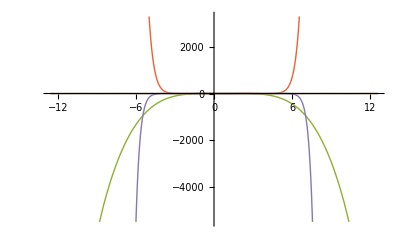

```mathematica
(* 31. f(x) = Cos[2x + (Pi/2)] *)
Clear[f,P1,P2,P3,x]
f[x_]:= Cos[2x + (Pi/2)];
c=Pi/4;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4 * Pi, 4 * Pi},PlotStyle->Thick]
```

1+x/2

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768+(715 x^9)/65536-(2431 x^10)/262144+(4199 x^11)/524288-(29393 x^12)/4194304+(52003 x^13)/8388608-(185725 x^14)/33554432+(334305 x^15)/67108864

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768+(715 x^9)/65536-(2431 x^10)/262144+(4199 x^11)/524288-(29393 x^12)/4194304+(52003 x^13)/8388608-(185725 x^14)/33554432+(334305 x^15)/67108864-(9694845 x^16)/2147483648+(17678835 x^17)/4294967296-(64822395 x^18)/17179869184+(119409675 x^19)/34359738368-(883631595 x^20)/274877906944

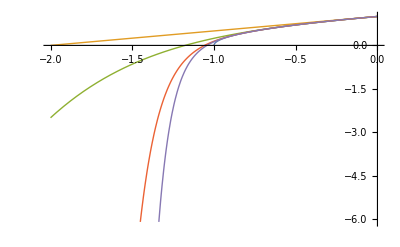

```mathematica
(* 32. f(x) = Sqrt[x+1] *)
Clear[f,P1,P2,P3,x]
f[x_]:= Sqrt[x+1];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-2,0},PlotStyle->Thick]
```